```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/FEinterpolants.nb"]
```

```mathematica
oDir=NotebookDirectory[];
SetDirectory@oDir;
```

## Величины, входящие в уравнение

```mathematica
initialMesh=import@"mesh_0.ntnr";
```

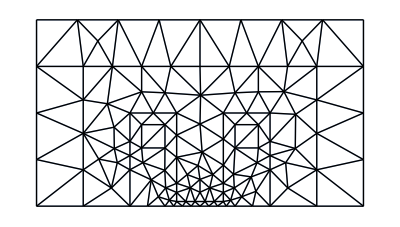

```mathematica
highlight[initialMesh,{},0]
```

### Плотность распределения тока J_z и кэффициент диффузии 1/(μ_0 μ̂)

```mathematica
FE=ΔP0L;
```

```mathematica
force=Import["force.dat"][[1]];
diffusion=Import["diffusion.dat"][[1]];
```

```mathematica
forceInterp=𝒫[force,FE,initialMesh];
diffusionInterp=𝒫[diffusion,FE,initialMesh];
```

```mathematica
densityPlot𝒫ξ[forceInterp,initialMesh,{Min@force,Max@force},"TemperatureMap",True]
densityPlot𝒫ξ[diffusionInterp,initialMesh,{Min@diffusion,Max@diffusion},"TemperatureMap",True]
```

-Graphics-

-Graphics-

## Решение линейной задачи

```mathematica
mesh=import@"mesh.ntnr";
```

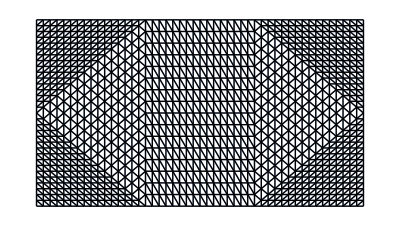

```mathematica
highlight[mesh,{},0]
```

```mathematica
FE=ΔP2L;
```

```mathematica
xLinear=Import["x_linear.dat"][[1]];
BxLinear=Import["Bx_linear.dat"][[1]];
ByLinear=Import["By_linear.dat"][[1]];
BnLinear=Import["Bn_linear.dat"][[1]];
```

```mathematica
xLinearFastInterp=interpolantOfξ[xLinear,FE,mesh];
```

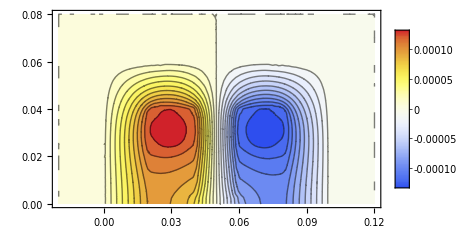

```mathematica
ContourPlot[xLinearFastInterp[x,y],{x,y}∈Ω,AspectRatio->Automatic,ColorFunction->"TemperatureMap",PlotLegends->Automatic,
Contours->23,
PlotPoints->45
]
```

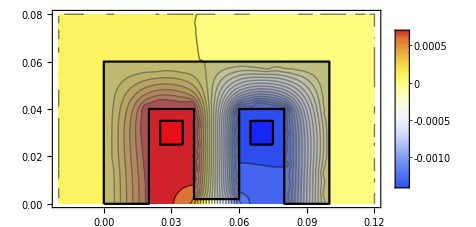

```mathematica
Show[ContourPlot[xLinearFastInterp[x,y],{x,y}∈Ω,AspectRatio->Automatic,ColorFunction->"TemperatureMap",PlotLegends->Automatic,
Contours->21,
PlotPoints->100,
MaxRecursion->0
],
Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet]
]
```

```mathematica
BnLinearFastInterp=interpolantOfξ[BnLinear,FE,mesh];
BxLinearFastInterp=interpolantOfξ[BxLinear,FE,mesh];
ByLinearFastInterp=interpolantOfξ[ByLinear,FE,mesh];
BLinearFastInterp[x_,y_]:={
BxLinearFastInterp[x,y],
ByLinearFastInterp[x,y]
}
```

```mathematica
BFieldLinear=Show[
StreamDensityPlot[BLinearFastInterp[x,y],{x,y}∈Subscript[Ω, default],
ColorFunction->"DeepSeaColors",StreamStyle->Blue,
PlotLegends->Automatic,
AspectRatio->Automatic,StreamPoints->Fine],
Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet],
ImageSize->400
]
```

```mathematica
Export["../../LaTeX/img/b_linear.pdf",BFieldLinear]
```

```mathematica
meanLinear=Quiet@NIntegrate[Norm@BLinearFastInterp[x,y],{x,y}∈Subscript[Ω, field]]/Area@Subscript[Ω, field]
```

```mathematica
sigmaLinear=Quiet@Sqrt[NIntegrate[(Norm@BLinearFastInterp[x,y]-mean)^2,{x,y}∈Subscript[Ω, field]]/Area@Subscript[Ω, field]]
```

```mathematica
LBJ={L6,L7,L8,L9,L10,L11}={0.059548313507409474,0.5954831329632132,5.954831311018183,59.548313266856084,595.4831359570154,5954.831369824995};
```

```mathematica
{S40,S2}={595.3356180749454,595.3106000489369};
```

## Решение нелинейной задачи

```mathematica
xNonlinear=Import["x_nonlinear.dat"][[1]];
BxNonlinear=Import["Bx_nonlinear.dat"][[1]];
ByNonlinear=Import["By_nonlinear.dat"][[1]];
BnNonlinear=Import["Bn_nonlinear.dat"][[1]];
```

```mathematica
xNonlinearFastInterp=interpolantOfξ[xNonlinear,FE,mesh];
```

```mathematica
ANonlinearPlot=Show[ContourPlot[xNonlinearFastInterp[x,y],{x,y}∈Subscript[Ω, default],AspectRatio->Automatic,ColorFunction->"TemperatureMap",PlotLegends->Automatic,
Contours->21,
PlotPoints->100,
MaxRecursion->0
],
Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet],
ImageSize->400
]
```

```mathematica
Export["../../LaTeX/img/a_nonlinear_11.pdf",ANonlinearPlot]
```

```mathematica
BnNonlinearFastInterp=interpolantOfξ[BnNonlinear,FE,mesh];
BxNonlinearFastInterp=interpolantOfξ[BxNonlinear,FE,mesh];
ByNonlinearFastInterp=interpolantOfξ[ByNonlinear,FE,mesh];
BNonlinearFastInterp[x_,y_]:={
BxNonlinearFastInterp[x,y],
ByNonlinearFastInterp[x,y]
}
```

```mathematica
BFieldNonlinear=Show[
StreamDensityPlot[BNonlinearFastInterp[x,y],{x,y}∈Subscript[Ω, default],
ColorFunction->"DeepSeaColors",StreamStyle->Blue,
PlotLegends->Automatic,
AspectRatio->Automatic,StreamPoints->Fine],
Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet],
ImageSize->400
]
```

```mathematica
Export["../../LaTeX/img/b_nonlinear.pdf",BFieldNonlinear];
```

```mathematica
meanNonlinear=Quiet@NIntegrate[Norm@BNonlinearFastInterp[x,y],{x,y}∈Subscript[Ω, field]]/Area@Subscript[Ω, field]
```

```mathematica
sigmaNonlinear=Quiet@Sqrt[NIntegrate[(Norm@BNonlinearFastInterp[x,y]-meanNonlinear)^2,{x,y}∈Subscript[Ω, field]]/Area@Subscript[Ω, field]]
```

```mathematica
100*0.13349527572954056/13.798343489215108
```

```mathematica
{SN40,SN30,SN20,SN10,SN8,SN6,SN4,SN2}={13.942192783768355,13.901647237652748,13.803379679932856,13.449446375883769,13.269565200063205,12.984300091127958,12.493595095783803,11.551587727281094};
```

```mathematica
NBJ={NB6,NB7,NB8,NB9,NB10,NB11}={0.060851905719385146,0.6163611168129154,1.709683950099388,3.0754663913034617,13.798343489215108,121.39699636305616};
```

## Зависимость магнитного поля от плотности тока

```mathematica
LBJ=Table[{10^i,LBJ[[i-5]]},{i,6,11}];
NBJ=Table[{10^i,NBJ[[i-5]]},{i,6,11}];
```

```mathematica
plotBJlinear=ListLinePlot[LBJ[[;;5]],PlotMarkers->{{"●",10}},PlotStyle->Blue,PlotRange->All]
```

```mathematica
plotBJ=ListLinePlot[{LBJ[[;;3]],NBJ[[;;3]]},PlotMarkers->{{"●",10},{"▲",10}},PlotStyle->{Blue,Red},PlotRange->All,PlotLegends->{"линейная задача","нелинейная задача"}]
```

```mathematica
plotBJnonlinear=ListLinePlot[NBJ[[;;5]],PlotMarkers->{{"▲",10}},PlotStyle->Red,PlotRange->All]
```

```mathematica
Export["../../LaTeX/img/bj.pdf",plotBJ];
```

```mathematica
Export["../../LaTeX/img/bj_linear.pdf",plotBJlinear];
```

```mathematica
Export["../../LaTeX/img/bj_nonlinear.pdf",plotBJnonlinear];
```

## Telma

```mathematica
Export["telmaNodes.dat",Prepend[nodes,{Length@nodes}]];
```

```mathematica
(* посчитать в тельме… *)
```

```mathematica
data=Import["RESB","Data"];
```

```mathematica
BxTelma={#[[2]],#[[4]],#[[6]]}&/@(ToExpression@StringReplace[StringTrim@StringSplit[#,{"  ","="}],"E"->"*10^"]&/@data);
ByTelma={#[[2]],#[[4]],#[[8]]}&/@(ToExpression@StringReplace[StringTrim@StringSplit[#,{"  ","="}],"E"->"*10^"]&/@data);
```

```mathematica
BxTelmaFastInterp=Interpolation[BxTelma,InterpolationOrder->1];
ByTelmaFastInterp=Interpolation[ByTelma,InterpolationOrder->1];
BTelmaFastInterp[x_,y_]:={
BxTelmaFastInterp[x,y],
ByTelmaFastInterp[x,y]
}
```

```mathematica
BFieldTelma=Show[
StreamDensityPlot[BTelmaFastInterp[x,y],{x,y}∈Subscript[Ω, default],
ColorFunction->"DeepSeaColors",StreamStyle->Blue,
PlotLegends->Automatic,
AspectRatio->Automatic,StreamPoints->Fine],
Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet],
ImageSize->400
]
```

```mathematica
Export["../../LaTeX/img/b_linear_telma.pdf",BFieldLinear]
```

```mathematica
Quiet@Sqrt@NIntegrate[(Norm@BTelmaFastInterp[x,y]-Norm@BLinearFastInterp[x,y])^2,{x,y}∈Subscript[Ω, field]]
```

```mathematica
0.379832370252335/mean
```

```mathematica
ContourPlot[xLinearFastInterp[x,y],{x,y}∈Ω,AspectRatio->Automatic,ColorFunction->"TemperatureMap",PlotLegends->Automatic,
Contours->21,
PlotPoints->100,
MaxRecursion->0
]
```